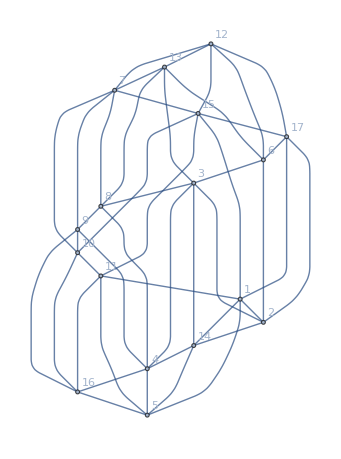
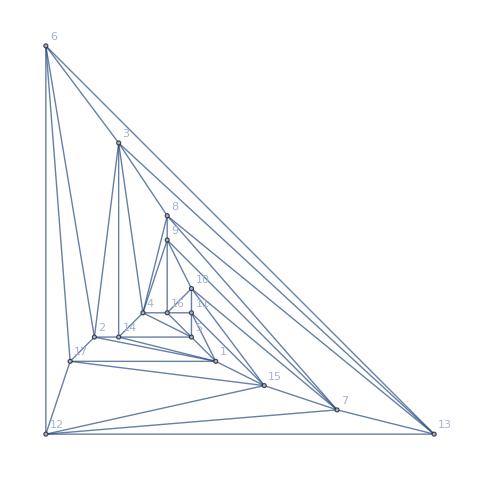
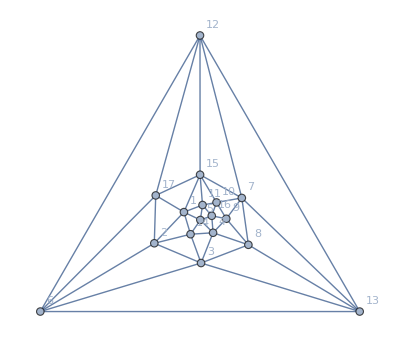

```mathematica
Table[Graph[plantri8,GraphLayout->layout],{layout,{"LayeredDigraphEmbedding","PlanarEmbedding","TutteEmbedding"}}]
```

```mathematica
ch=ChromaticPolynomial[plantri8]
```

Function[x,71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17]

```mathematica
BellB[17]
```

82864869804

```mathematica
VertexCount[plantri8]
```

17

```mathematica
EdgeCount[plantri8]
```

45

```mathematica
ch[4]/24
```

22

```mathematica
StirlingS2[17,4]
```

694337290

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[VertexDelete[plantri8,14],x]]
```

{0,0,0,0,63,31366,906909,5851378,13552503,14251874,7761732,2362156,417968,43395,2575,80,1}

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[plantri8,x]]
```

{0,0,0,0,22,36281,1796800,17198421,55339513,78241812,56479726,22766977,5401613,773706,66900,3380,91,1}

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[plantri8,x]]//Total
```

238105243

```mathematica
Length[EdgeList[GraphComplement[plantri8]]]
```

91

```mathematica
Table[(allGraphs5[k,"colofour"]/.RepGraph["C"])->(allGraphs5[k,"colofour"]/.RepEmbed["C"]),{k,alfa1s}]
```

{-Graphics-361660→3,-Graphics-317380→8,-Graphics-296080→0,-Graphics-361120→8,-Graphics-317140→3}

```mathematica
alfa1s
```

{36166,31738,29608,36112,31714}

```mathematica
Table[EdgeCycleMatrix[plantri8,v],{v,VertexList[plantri8]}]
```

```mathematica
Table[VertexDegree[plantri8,v],{v,VertexList[plantri8]}]
```

{5,5,6,6,5,5,6,5,5,5,5,6,5,5,6,5,5}

```mathematica
EdgeCycleMatrix[plantri8]//MatrixRank
```

29